```mathematica
Simplify[((ⅇ^y+ⅇ^-y)/2 Sin[x])^2+((ⅇ^-y-ⅇ^y)/2 Cos[x])^2]
```

1/4 (ⅇ^(-2 y)+ⅇ^(2 y)-2 Cos[x]^2+2 Sin[x]^2)

```mathematica
Reduce[(ⅇ^(-2x)+ⅇ^(2x))/4-1/2>=0,x,Reals]
```

True

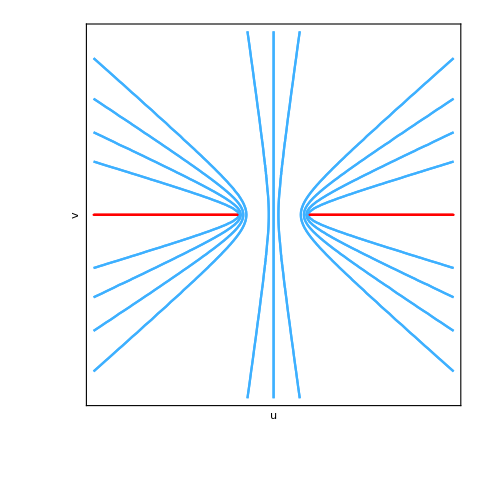

```mathematica
g1=Table[
ContourPlot[
(u/(Sin[a]+10^-10))^2-(v/(Cos[a]+10^-10))^2==1,{u,-5,5},{v,-5,5},
Axes->True,
AxesLabel->{u,v},
FrameTicks->None,
ImageSize->480,
ContourStyle->96],
{a,-5,5,1}];
g2=RegionPlot[x≤-1,{x,-5,-1},{y,-10^-10-10^-10,-10^-10+10^-10},BoundaryStyle->Red];
g3=RegionPlot[x≥1,{x,1,5},{y,-10^-10-10^-10,-10^-10+10^-10},BoundaryStyle->Red];
Show@@{g1,g2,g3}
```

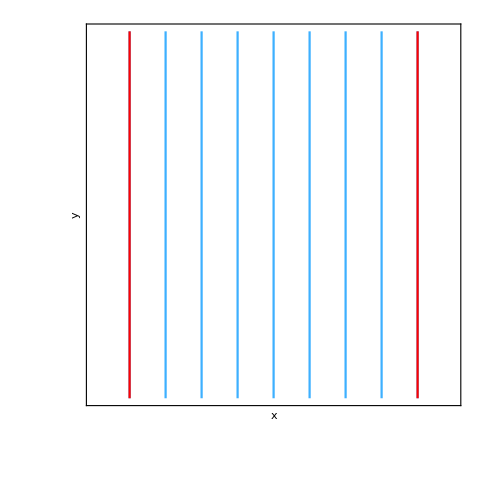

```mathematica
g11=Table[
ContourPlot[
x==a,{x,-5,5},{y,-5,5},
Axes->True,
AxesLabel->{x,y},
FrameTicks->None,
ImageSize->480,
ContourStyle->96],
{a,-5,5,1}];
g12=ContourPlot[
x==4,{x,-5,5},{y,-5,5},
Axes->True,
AxesLabel->{x,y},
FrameTicks->None,
ImageSize->480,
ContourStyle->Red];
g13=ContourPlot[
x==-4,{x,-5,5},{y,-5,5},
Axes->True,
AxesLabel->{x,y},
FrameTicks->None,
ImageSize->480,
ContourStyle->Red];
Show@@{g11,g12,g13}
Export[FileNameJoin[{NotebookDirectory[],"sin_map_w"<>".eps"}],Show@@{g11,g12,g13}]
```

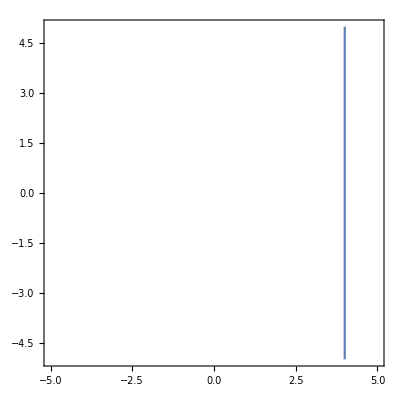

```mathematica
ContourPlot[t==4,{t,-5,5},{y,-5,5}]
```